```mathematica
(*Sphere with Bumps-Stage 2:Emerging Knowledge Hills*)R=1;
ParametricPlot3D[{R*(1+0.2*Sin[3 u]*Sin[4 v])*Cos[u]*Sin[v],R*(1+0.2*Sin[3 u]*Sin[4 v])*Sin[u]*Sin[v],R*(1+0.2*Sin[3 u]*Sin[4 v])*Cos[v]},{u,0,2*Pi},(*Azimuthal angle*){v,0,Pi},(*Polar angle*)PlotStyle->{Opacity[0.7],ColorData["Pastel"]["LightBlue"]},(*Soft,varied color*)Mesh->15,(*Slightly refined mesh for school phase*)MeshStyle->Directive[Thin,Gray],(*Bold lines,improving style*)Axes->True,AxesLabel->{"x","y","z"},Boxed->False,PlotRange->{{-1.5,1.5},{-1.5,1.5},{-1.5,1.5}},ViewPoint->{2,-2,1},ImageSize->Medium,PlotLabel->Style["Stage 2: Sphere with Knowledge Hills",Bold,12]]
```

-Graphics3D-

```mathematica
(*Smooth Sphere-Stage 1:Childish Unified Knowledge*)R=1; (*Radius of the sphere*)
ParametricPlot3D[{R*Cos[u]*Sin[v],R*Sin[u]*Sin[v],R*Cos[v]},{u,0,2*Pi},(*Azimuthal angle*){v,0,Pi},(*Polar angle*)PlotStyle->{Opacity[0.7],ColorData["Pastel"]["MistyRose"]},(*Soft,childish color*)Mesh->10,(*Coarse mesh for childish style*)MeshStyle->Directive[Thin,Gray],(*Bold,simple lines*)Axes->True,AxesLabel->{"x","y","z"},Boxed->False,PlotRange->{{-1.5,1.5},{-1.5,1.5},{-1.5,1.5}},ViewPoint->{2,-2,1},ImageSize->Medium,PlotLabel->Style["Stage 1: Childish Sphere",Bold,12]]
```

-Graphics3D-

```mathematica
(*Stage 2:Emerging Knowledge Hills-Now in Glorious Technicolor*)R=1;
ParametricPlot3D[{R*(1+0.3*Sin[3*u]*Sin[4*v])*Cos[u]*Sin[v],R*(1+0.3*Sin[3*u]*Sin[4*v])*Sin[u]*Sin[v],R*(1+0.3*Sin[3*u]*Sin[4*v])*Cos[v]},{u,0,2*Pi},{v,0,Pi},ColorFunction->Function[{x,y,z,u,v},ColorData["Rainbow"][0.5+0.5*Sin[3*u]*Sin[4*v]]],ColorFunctionScaling->False,PlotStyle->Opacity[0.9],Mesh->15,MeshStyle->Directive[Thin,Gray],Axes->False,Boxed->False,PlotRange->{{-1.5,1.5},{-1.5,1.5},{-1.5,1.5}},ViewPoint->{2,-2,1},ImageSize->Large,PlotLabel->Style["Stage 2: Cognitive Diversity Emerging",Bold,14],Background->White]
```

-Graphics3D-

```mathematica
(*Distinct Knowledge Domains*)R=1;
ParametricPlot3D[{R*(1+0.35*Sin[3*u]*Sin[4*v])*Cos[u]*Sin[v],R*(1+0.35*Sin[3*u]*Sin[4*v])*Sin[u]*Sin[v],R*(1+0.35*Sin[3*u]*Sin[4*v])*Cos[v]},{u,0,2*Pi},{v,0,Pi},ColorFunction->Function[{x,y,z,u,v},Hue[Mod[Floor[3*u/(2*Pi)]+Floor[4*v/Pi],7]/7,0.8,0.9+0.1*Sin[3*u]*Sin[4*v]]],ColorFunctionScaling->False,PlotStyle->Opacity[0.95],Mesh->{12,8},MeshStyle->Directive[Thin,Gray],Axes->False,Boxed->False,Lighting->"Neutral",PlotRange->{{-1.5,1.5},{-1.5,1.5},{-1.5,1.5}},ViewPoint->{2,-2,1.5},ImageSize->Large,PlotLabel->Style["The Beautiful Lie of Balanced Education",Bold,16],Background->White]
```

-Graphics3D-

```mathematica
(*Stage 2:Emerging Knowledge Hills-With Grid Lines*)R=1;
ParametricPlot3D[{R*(1+0.3*Sin[3*u]*Sin[4*v])*Cos[u]*Sin[v],R*(1+0.3*Sin[3*u]*Sin[4*v])*Sin[u]*Sin[v],R*(1+0.3*Sin[3*u]*Sin[4*v])*Cos[v]},{u,0,2*Pi},{v,0,Pi},ColorFunction->Function[{x,y,z,u,v},ColorData["Rainbow"][0.5+0.5*Sin[3*u]*Sin[4*v]]],ColorFunctionScaling->False,PlotStyle->Opacity[0.9],Mesh->{15,10},(*This adds the grid back*)MeshStyle->Directive[Thin,Gray],(*Makes grid visible*)Axes->True,(*Adds the axis back if you want them*)AxesLabel->{"x","y","z"},Boxed->False,PlotRange->{{-1.5,1.5},{-1.5,1.5},{-1.5,1.5}},ViewPoint->{2,-2,1},ImageSize->Large,PlotLabel->Style["Stage 2: Cognitive Diversity Emerging",Bold,14]]
```

-Graphics3D-

```mathematica
(*Stage 3:Specialization Mountains-The Great Separation*)R=0.4;  (*Shrinking base sphere*)
ParametricPlot3D[{(R+0.8*Abs[Sin[2*u]*Sin[2*v]]^3)*Cos[u]*Sin[v],(R+0.8*Abs[Sin[2*u]*Sin[2*v]]^3)*Sin[u]*Sin[v],(R+0.8*Abs[Sin[2*u]*Sin[2*v]]^3)*Cos[v]},{u,0,2*Pi},{v,0,Pi},ColorFunction->Function[{x,y,z,u,v},ColorData["Rainbow"][1-Abs[Sin[2*u]*Sin[2*v]]^2  (*Colors fade in valleys*)]],ColorFunctionScaling->False,PlotStyle->Opacity[0.95],Mesh->{12,8},MeshStyle->Directive[Thickness[0.002],GrayLevel[0.3]],Axes->True,AxesLabel->{"x","y","z"},Boxed->False,PlotRange->{{-1.5,1.5},{-1.5,1.5},{-1.5,1.5}},ViewPoint->{2,-2,1},ImageSize->Large,PlotLabel->Style["Stage 3: The Specialization Mountains",Bold,14],Lighting->{{"Ambient",GrayLevel[0.5]},{"Directional",White,{{2,-2,2},{0,0,0}}}}]
```

-Graphics3D-

```mathematica
(*Stage 3:Unequal Peaks-Because STEM Gets All The Funding*)R=0.3;
ParametricPlot3D[{(R+0.9*Abs[Sin[2*u]*Sin[v]]^2+(*Major peak 1-STEM*)0.6*Abs[Sin[3*u]*Sin[2*v]]^2+(*Medium peaks-Business/Law*)0.3*Abs[Cos[4*u]*Sin[3*v]]^2+(*Small peaks-Humanities*)0.15*Sin[5*u]^2*Sin[4*v]^2             (*Tiny bumps-Arts*))*Cos[u]*Sin[v],(R+0.9*Abs[Sin[2*u]*Sin[v]]^2+0.6*Abs[Sin[3*u]*Sin[2*v]]^2+0.3*Abs[Cos[4*u]*Sin[3*v]]^2+0.15*Sin[5*u]^2*Sin[4*v]^2)*Sin[u]*Sin[v],(R+0.9*Abs[Sin[2*u]*Sin[v]]^2+0.6*Abs[Sin[3*u]*Sin[2*v]]^2+0.3*Abs[Cos[4*u]*Sin[3*v]]^2+0.15*Sin[5*u]^2*Sin[4*v]^2)*Cos[v]},{u,0,2*Pi},{v,0,Pi},ColorFunction->Function[{x,y,z,u,v},ColorData["Rainbow"][0.2+0.8*(Norm[{x,y,z}]-0.3)/1.5  (*Color by height*)]],ColorFunctionScaling->False,PlotStyle->Opacity[0.95],Mesh->{15,10},MeshStyle->Directive[Thickness[0.001],Black],Axes->True,AxesLabel->{"x","y","z"},Boxed->False,PlotRange->{{-2,2},{-2,2},{-2,2}},ViewPoint->{2,-2,1},ImageSize->Large,PlotLabel->Style["Stage 3: The Hierarchy of Specialization",Bold,14]]
```

-Graphics3D-

```mathematica
(*Stage 3b:Market-Value-Based Peak Heights*)R=0.25;
ParametricPlot3D[{(R+1.2*Exp[-3*((u-Pi/3)^2+(v-Pi/3)^2)]+(*Tech/CS-Tallest*)0.9*Exp[-3*((u-Pi)^2+(v-Pi/2)^2)]+(*Finance-Second*)0.7*Exp[-3*((u-5*Pi/3)^2+(v-2*Pi/3)^2)]+(*Medicine-Third*)0.5*Exp[-4*((u-2*Pi/3)^2+(v-Pi/4)^2)]+(*Engineering*)0.3*Exp[-5*((u-4*Pi/3)^2+(v-3*Pi/4)^2)]+(*Law*)0.2*Exp[-5*((u-Pi/2)^2+(v-Pi/6)^2)]+(*Psychology*)0.1*Exp[-6*((u-3*Pi/2)^2+(v-5*Pi/6)^2)]    (*Philosophy-RIP*))*Cos[u]*Sin[v],(R+1.2*Exp[-3*((u-Pi/3)^2+(v-Pi/3)^2)]+0.9*Exp[-3*((u-Pi)^2+(v-Pi/2)^2)]+0.7*Exp[-3*((u-5*Pi/3)^2+(v-2*Pi/3)^2)]+0.5*Exp[-4*((u-2*Pi/3)^2+(v-Pi/4)^2)]+0.3*Exp[-5*((u-4*Pi/3)^2+(v-3*Pi/4)^2)]+0.2*Exp[-5*((u-Pi/2)^2+(v-Pi/6)^2)]+0.1*Exp[-6*((u-3*Pi/2)^2+(v-5*Pi/6)^2)])*Sin[u]*Sin[v],(R+1.2*Exp[-3*((u-Pi/3)^2+(v-Pi/3)^2)]+0.9*Exp[-3*((u-Pi)^2+(v-Pi/2)^2)]+0.7*Exp[-3*((u-5*Pi/3)^2+(v-2*Pi/3)^2)]+0.5*Exp[-4*((u-2*Pi/3)^2+(v-Pi/4)^2)]+0.3*Exp[-5*((u-4*Pi/3)^2+(v-3*Pi/4)^2)]+0.2*Exp[-5*((u-Pi/2)^2+(v-Pi/6)^2)]+0.1*Exp[-6*((u-3*Pi/2)^2+(v-5*Pi/6)^2)])*Cos[v]},{u,0,2*Pi},{v,0,Pi},ColorFunction->Function[{x,y,z,u,v},Which[Norm[{x,y,z}]>1.2,ColorData["Rainbow"][0.95],(*Tech=Red/Hot*)Norm[{x,y,z}]>0.9,ColorData["Rainbow"][0.7],(*Finance=Orange*)Norm[{x,y,z}]>0.6,ColorData["Rainbow"][0.5],(*Medicine=Green*)Norm[{x,y,z}]>0.4,ColorData["Rainbow"][0.3],(*Engineering=Blue*)True,GrayLevel[0.4]                                 (*Humanities=Gray*)]],ColorFunctionScaling->False,PlotStyle->Opacity[0.95],Mesh->{12,8},MeshStyle->Directive[Thin,GrayLevel[0.2]],Axes->False,Boxed->False,PlotRange->{{-2,2},{-2,2},{-2,2}},ViewPoint->{2.5,-2.5,1.5},ImageSize->Large,PlotLabel->Style["Stage 3: Specialization by Market Value (2025 Edition)",Bold,14],Background->White]
```

-Graphics3D-

```mathematica
(*Stage 4:The Single Vector-Cognitive Death*)ParametricPlot3D[{0.05*Cos[u]+t*0.02*Sin[u],0.05*Sin[u]-t*0.02*Cos[u],t},{u,0,2*Pi},{t,-1.5,1.5},ColorFunction->Function[{x,y,z,u,t},GrayLevel[0.3+0.4*(1-Abs[t]/1.5)]  (*Fading to gray*)],ColorFunctionScaling->False,PlotStyle->Opacity[0.9],Mesh->{20,15},MeshStyle->Directive[Thin,Black],Axes->True,AxesLabel->{"","","Specialization"},Boxed->False,PlotRange->{{-1.5,1.5},{-1.5,1.5},{-1.5,1.5}},ViewPoint->{2,-2,0.5},ImageSize->Large,PlotLabel->Style["Stage 4: The Vector - One Direction, No Alternatives",Bold,14],Background->White]
```

-Graphics3D-

```mathematica
(*Stage 4c:The Vector with Everything Lost*)Graphics3D[{(*The vector*){Gray,Opacity[0.8],Cylinder[{{0,0,-2},{0,0,2}},0.03]},{Red,Sphere[{0,0,2},0.05]},(*The specialized tip*)(*Ghost spheres showing what was lost*){Opacity[0.1],Table[Sphere[{0.5*Cos[i],0.5*Sin[i],0},0.1],{i,0,2*Pi,Pi/4}]},(*Labels*)Text[Style["All Other Knowledge",Gray,10],{1,0,0}],Text[Style["Lost Connections",Gray,10],{-1,0,0.5}],Text[Style["YOUR SPECIALTY",Red,Bold,12],{0,0,2.3}],Text[Style["Nothing Else Remains",Gray,Italic,10],{0,0,-2.3}]},Boxed->False,Axes->True,AxesLabel->{"Dead","Dead","Career"},PlotRange->{{-2,2},{-2,2},{-2.5,2.5}},ViewPoint->{2,-2,0.5},ImageSize->Large,PlotLabel->Style["Welcome to Your Future: A Needle Awaiting AI Replacement",Bold,16],Background->White,Lighting->"Dramatic"]
```

-Graphics3D-

```mathematica
(*Clear any previous definitions*)ClearAll[ResistanceR,EnergyInvest,CognitiveTypes,EfficiencyZ,CognitiveSov]

(*Resistance to Extraction-Core measure*)
ResistanceR[t_]:=Piecewise[{{0.95,t<1088},{0.95-0.05*(t-(-500))/1588,-500<=t<1088},{0.90-0.20*(t-1088)/(1750-1088),1088<=t<1750},{0.70-0.20*(t-1750)/(1920-1750),1750<=t<1920},{0.50-0.25*(t-1920)/(1999-1920),1920<=t<1999},{0.25-0.20*(t-1999)/(2020-1999),1999<=t<2020},{0.05*Exp[-0.1*(t-2020)],t>=2020}}]

(*Energy Investment in years*)
EnergyInvest[t_]:=Piecewise[{{25,t<1088},{10,1088<=t<1750},{5,1750<=t<1920},{4.5,1920<=t<1999},{2.5,1999<=t<2020},{0.014*Exp[-0.05*(t-2020)],t>=2020}}]

(*Cognitive Diversity-Number of knowledge types*)
CognitiveTypes[t_]:=Piecewise[{{18,t<1088},{18-6*(t-(-500))/1588,-500<=t<1088},{12-5*(t-1088)/(1920-1088),1088<=t<1920},{7-4*(t-1920)/(1999-1920),1920<=t<1999},{3-1.5*(t-1999)/(2020-1999),1999<=t<2020},{1.5*Exp[-0.1*(t-2020)],t>=2020}}]

(*Efficiency (Z-axis)-declining effectiveness*)
EfficiencyZ[t_]:=Piecewise[{{0.8,t<1750},{0.8-0.2*(t-1750)/(1999-1750),1750<=t<1999},{0.6-0.5*(t-1999)/(2020-1999),1999<=t<2020},{0.1*Exp[-0.1*(t-2020)],t>=2020}}]

(*Cognitive Sovereignty-full equation*)
(*Sovereignty=(Energy/Time)×Resistance×Efficiency*)
CognitiveSov[t_,z_]:=EnergyInvest[t]*ResistanceR[t]*z
```

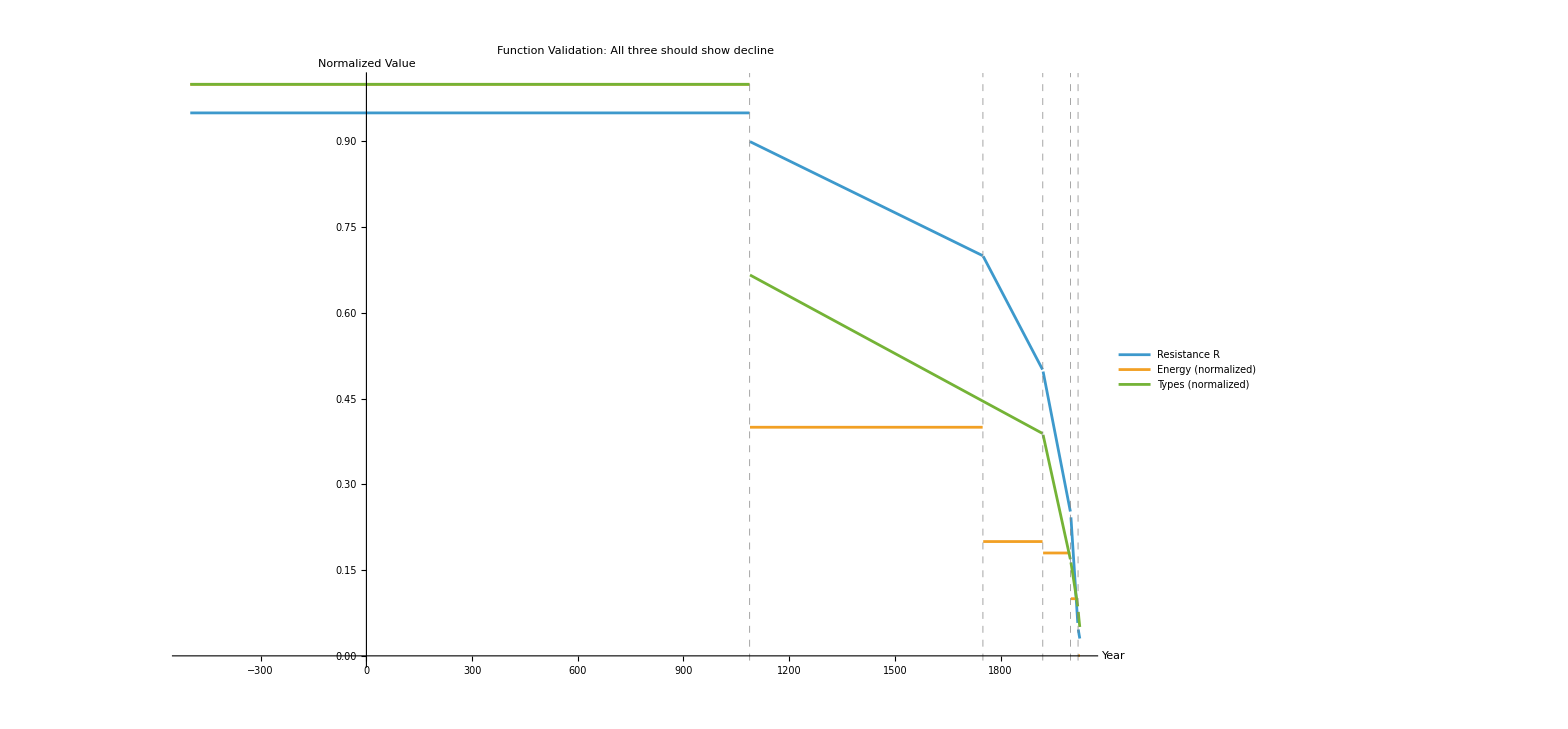

```mathematica
(*Quick validation-plot key functions*)Plot[{ResistanceR[t],EnergyInvest[t]/25,CognitiveTypes[t]/18},{t,-500,2025},PlotLegends->{"Resistance R","Energy (normalized)","Types (normalized)"},PlotLabel->"Function Validation: All three should show decline",AxesLabel->{"Year","Normalized Value"},GridLines->{{1088,1750,1920,1999,2020},None},GridLinesStyle->Directive[Gray,Dashed],PlotRange->All,ImageSize->Large]
```

```mathematica
(* =====COGNITIVE DEVOLUTION:THERMODYNAMIC VISUALIZATION=====*)(*Clear workspace*)ClearAll["Global`*"]

(* ===CORE FUNCTIONS===*)

ResistanceR[t_]:=Piecewise[{{0.95,t<1088},{0.95-0.05*(t+500)/1588,-500<=t<1088},{0.90-0.20*(t-1088)/(1750-1088),1088<=t<1750},{0.70-0.20*(t-1750)/(1920-1750),1750<=t<1920},{0.50-0.25*(t-1920)/(1999-1920),1920<=t<1999},{0.25-0.20*(t-1999)/(2020-1999),1999<=t<2020},{0.05*Exp[-0.1*(t-2020)],t>=2020}}]

EnergyInvest[t_]:=Piecewise[{{25,t<1088},{10,1088<=t<1750},{5,1750<=t<1920},{4.5,1920<=t<1999},{2.5,1999<=t<2020},{0.014*Exp[-0.05*(t-2020)],t>=2020}}]

CognitiveTypes[t_]:=Piecewise[{{18,t<1088},{18-6*(t+500)/1588,-500<=t<1088},{12-5*(t-1088)/(1920-1088),1088<=t<1920},{7-4*(t-1920)/(1999-1920),1920<=t<1999},{3-1.5*(t-1999)/(2020-1999),1999<=t<2020},{1.5*Exp[-0.1*(t-2020)],t>=2020}}]

CognitiveSov[t_,z_]:=EnergyInvest[t]*ResistanceR[t]*z

(* ===COLOR FUNCTION===*)

colorFunc[r_?NumericQ]:=Which[r>=0.9,RGBColor[148/255,0/255,211/255],r>=0.7,Blend[{RGBColor[148/255,0/255,211/255],Blue},(0.9-r)/0.2],r>=0.5,Blend[{Blue,Green},(0.7-r)/0.2],r>=0.3,Blend[{Green,Yellow},(0.5-r)/0.2],r>=0.1,Blend[{Yellow,Orange},(0.3-r)/0.2],True,Blend[{Orange,Red},Max[0,Min[1,(0.1-r)/0.1]]]]

(* ===GENERATE ALL FIGURES===*)

fig2a=Plot3D[ResistanceR[t],{t,-500,2025},{z,0,1},ColorFunction->Function[{t,z,r},colorFunc[r]],ColorFunctionScaling->False,PlotLabel->"Figure 2a: Resistance to Extraction",AxesLabel->{"Year","Efficiency","R"},PlotPoints->80,ImageSize->Large]

(*Add remaining figures...*)
```

-Graphics3D-

```mathematica
(* =====FIGURE 2A:RESISTANCE TO EXTRACTION=====*)fig2a=Plot3D[ResistanceR[t],{t,-500,2025},{z,0,1},ColorFunction->Function[{t,z,r},colorFunc[r]],ColorFunctionScaling->False,AxesLabel->{Style["Time (Year)",12,Bold],Style["Efficiency",12,Bold],Style["R (Architecture Quality)",12,Bold]},PlotLabel->Style["Figure 2a: Resistance to Extraction Collapse\n2,500 Years of Cognitive Architecture Degradation",14,Bold,Black],Mesh->None,PlotRange->All,BoxRatios->{2,1,1},ViewPoint->{1.3,-2.4,2},PlotPoints->80,MaxRecursion->2,ImageSize->Large,Lighting->"Neutral",PlotStyle->Directive[Opacity[0.9],Specularity[White,20]],Ticks->{{{-500,"-500\nAncient"},{1088,"1088\nMedieval"},{1750,"1750\nIndustrial"},{1999,"1999\nBologna"},{2020,"2020\nMicro"}},Automatic,Automatic}]

(*Display and export*)
fig2a
Export["Fig2a_Resistance.png",fig2a,ImageSize->2400,ImageResolution->300,Background->White]
```

-Graphics3D-

-Graphics3D-

Fig2a_Resistance.png

```mathematica
ClearAll["Global`*"]

(*Historical data points from Table 1*)
(*We'll interpolate between these*)

(*% Knowledge Workers over time*)
KnowledgeWorkers[t_]:=Which[t<=1800,0.01,t<=1950,0.01+(0.10-0.01)*(t-1800)/(1950-1800),t<=2024,0.10+(0.40-0.10)*(t-1950)/(2024-1950),t<=2040,0.40+(0.50-0.40)*(t-2024)/(2040-2024),t<=2060,0.50+(0.60-0.50)*(t-2040)/(2060-2040),True,0.60]

(*Resistance R over time*)
ResistanceR[t_]:=Which[t<=1800,0.80,t<=1950,0.80-(0.80-0.50)*(t-1800)/(1950-1800),t<=2024,0.50-(0.50-0.10)*(t-1950)/(2024-1950),t<=2040,0.10-(0.10-0.04)*(t-2024)/(2040-2024),t<=2060,0.04-(0.04-0.008)*(t-2040)/(2060-2040),True,0.008*Exp[-0.05*(t-2060)]]

(*Efficiency as function of Time AND % Knowledge Workers*)
(*Key insight:Higher % workers with lower R=efficiency collapse*)
Efficiency[t_,kwPct_]:=Module[{r=ResistanceR[t],baseEff},baseEff=Which[t<=1800,0.80,t<=1950,0.80-(0.80-0.50)*(t-1800)/(1950-1800),t<=2024,0.50-(0.50-0.10)*(t-1950)/(2024-1950),t<=2040,0.10-(0.10-0.04)*(t-2024)/(2040-2024),t<=2060,0.04-(0.04-0.01)*(t-2040)/(2060-2040),True,0.01*Exp[-0.05*(t-2060)]];
(*Efficiency decreases with more workers when R is low*)(*High R systems maintain efficiency even with scaling*)(*Low R systems collapse under their own weight*)baseEff*(1-0.5*(kwPct-KnowledgeWorkers[t])^2/0.6^2)]

(*Effective Power (the real output)*)
EffectivePower[t_,kwPct_]:=Module[{pop=Which[t<=1800,1,t<=1950,1+(2.5-1)*(t-1800)/(1950-1800),t<=2024,2.5+(8-2.5)*(t-1950)/(2024-1950),t<=2040,8+(9-8)*(t-2024)/(2040-2024),t<=2060,9+(10-9)*(t-2040)/(2060-2040),True,10],cogBudgetPerWorker=210  (*MW per billion knowledge workers*)},(*Total cognitive budget*)cogBudget=pop*kwPct*cogBudgetPerWorker;
(*Effective power=budget×efficiency*)cogBudget*Efficiency[t,kwPct]/1000  (*Convert to GW*)]
```

```mathematica
(*Figure 2A:The Efficiency Paradox*)fig2a=Plot3D[Efficiency[t,kw],{t,1800,2060},{kw,0.01,0.60},ColorFunction->Function[{t,kw,eff},Hue[0.7-0.7*eff,1,0.8]  (*Blue=high efficiency,Red=low*)],ColorFunctionScaling->False,AxesLabel->{Style["Time (Year)",12,Bold],Style["% Knowledge Workers",12,Bold],Style["Efficiency",12,Bold]},PlotLabel->Style["Figure 2: The Knowledge Worker Paradox\nMore Workers → Lower Efficiency (due to R collapse)",14,Bold],Mesh->15,MeshStyle->Directive[Gray,Opacity[0.3]],PlotPoints->80,PlotRange->All,BoxRatios->{2,1,1.5},ViewPoint->{-1.8,-2.2,1.5},ImageSize->Large,Lighting->"Neutral"]

fig2a
```

-Graphics3D-

```mathematica
fig2b=Plot3D[EffectivePower[t,kw],{t,1800,2060},{kw,0.01,0.60},ColorFunction->Function[{t,kw,power},Hue[0.65-0.6*Min[1,power/8],0.9,0.85]],ColorFunctionScaling->False,AxesLabel->{Style["Time (Year)",12,Bold],Style["% Knowledge Workers",12,Bold],Style["Effective Power (GW)",12,Bold]},PlotLabel->Style["Figure 3: Effective Cognitive Power\nPeak ~1980s, then collapse despite growing workforce",14,Bold],Mesh->15,MeshStyle->Directive[Gray,Opacity[0.3]],PlotPoints->80,PlotRange->All,BoxRatios->{2,1,1.5},ViewPoint->{-1.8,-2.2,1.5},ImageSize->Large,Lighting->"Neutral"]

fig2b
Export["Fig2b_EffectivePower.png",fig2b,ImageSize->2400,ImageResolution->300,Background->White]
```

-Graphics3D-

-Graphics3D-

Fig2b_EffectivePower.png

```mathematica
fig2c=Plot3D[ResistanceR[t],{t,1800,2060},{kw,0.01,0.60},ColorFunction->Function[{t,kw,r},Blend[{RGBColor[0.1,0,0.3],(*Dark purple:R=0*)RGBColor[0.8,0,0],(*Red:R=0.2*)RGBColor[1,0.5,0],(*Orange:R=0.4*)RGBColor[1,1,0],(*Yellow:R=0.6*)RGBColor[0,1,0],(*Green:R=0.8*)RGBColor[148/255,0,211/255] (*Violet:R=1.0*)},r]],ColorFunctionScaling->False,AxesLabel->{Style["Time (Year)",12,Bold],Style["% Knowledge Workers",12,Bold],Style["R (Architecture Quality)",12,Bold]},PlotLabel->Style["Figure 4: Resistance to Extraction Collapse\nIndependent of workforce size - pure architecture degradation",14,Bold],Mesh->15,MeshStyle->Directive[Gray,Opacity[0.3]],PlotPoints->80,PlotRange->All,BoxRatios->{2,1,1.5},ViewPoint->{-1.8,-2.2,1.5},ImageSize->Large,Lighting->"Neutral"]

fig2c
Export["Fig2c_Resistance.png",fig2c,ImageSize->2400,ImageResolution->300,Background->White]
```

-Graphics3D-

-Graphics3D-

Fig2c_Resistance.png

```mathematica
(*Efficiency per knowledge worker*)EfficiencyPerWorker[t_,kw_]:=If[kw>0.001,Efficiency[t,kw]/kw,0]

fig2d=Plot3D[EfficiencyPerWorker[t,kw],{t,1800,2060},{kw,0.01,0.60},ColorFunction->Function[{t,kw,epw},Hue[0.7-0.7*Min[1,epw/80],1,0.8]],ColorFunctionScaling->False,AxesLabel->{Style["Time (Year)",12,Bold],Style["% Knowledge Workers",12,Bold],Style["Efficiency per Worker",12,Bold]},PlotLabel->Style["Figure 5: Efficiency per Knowledge Worker\nCatastrophic per-capita collapse",14,Bold],Mesh->15,MeshStyle->Directive[Gray,Opacity[0.3]],PlotPoints->80,PlotRange->All,BoxRatios->{2,1,1.5},ViewPoint->{-1.8,-2.2,1.5},ImageSize->Large,Lighting->"Neutral"]

fig2d
Export["Fig2d_EfficiencyPerWorker.png",fig2d,ImageSize->2400,ImageResolution->300,Background->White]
```

-Graphics3D-

-Graphics3D-

Fig2d_EfficiencyPerWorker.png

```mathematica
(*Define the color for R=0.9 from our colorFunc*)sphereColor=Blend[{RGBColor[148/255,0/255,211/255],Blue},(0.9-0.9)/0.2]
(*This should give us the violet from R=0.9*)

(*Alternative:Just use the violet directly*)
sphereColor=RGBColor[148/255,0/255,211/255]

(*Create a beautiful sphere*)
sphereFig=Graphics3D[{(*Main sphere with R=0.9 color*)Opacity[0.85],Specularity[White,30],sphereColor,Sphere[{0,0,0},1],(*Optional:Add some mesh lines to show dimensionality*)Opacity[0.3],Thickness[0.003],Table[{sphereColor,Line[Table[{Cos[θ],Sin[θ]*Cos[φ],Sin[θ]*Sin[φ]},{θ,0,2π,π/20}]]},{φ,0,π,π/10}],Table[{sphereColor,Line[Table[{Cos[θ]*Sin[φ],Sin[θ]*Sin[φ],Cos[φ]},{θ,0,2π,π/20}]]},{φ,0,π,π/10}]},Lighting->"Neutral",Boxed->False,ViewPoint->{1.3,-2.4,2},ImageSize->Large,Background->White,PlotLabel->Style["Sphere Cognition: R = 0.9\nMultidimensional Architecture, Maximum Resistance to Extraction",14,Bold]]

sphereFig
Export["Sphere_R09.png",sphereFig,ImageSize->2400,ImageResolution->300,Background->White]
```

RGBColor[0.5803921568627451, 0., 0.8274509803921568]

RGBColor[Rational[148, 255], 0, Rational[211, 255]]

-Graphics3D-

-Graphics3D-

Sphere_R09.png

```mathematica
(*Pre-school:Natural sphere at R=0.9*)preschoolSphere=Graphics3D[{Opacity[0.9],Specularity[White,40],RGBColor[148/255,0/255,211/255],(*Pure violet*)Sphere[{0,0,0},1],(*Subtle organic texture*)Opacity[0.15],White,Table[Sphere[RandomPoint[Sphere[]],0.05],{50}]},Lighting->{{"Ambient",White},{"Directional",White,ImageScaled[{2,0,2}]},{"Directional",RGBColor[148/255,0/255,211/255],ImageScaled[{-2,-2,2}]}},Boxed->False,ViewPoint->{1.3,-2.4,2},ImageSize->800,PlotLabel->Style["Age 5: Natural Cognition\nR = 0.9 (Violet)\nInfinite curiosity, cross-domain connection",12,Bold]]

(*Post-school:Damaged sphere R=0.5-0.7*)
postschoolSphere=Show[schoolDamagedSphere,PlotLabel->Style["Age 22: Post-University\nR = 0.5-0.7 (Yellow-Orange)\n'Educated' = Standardized",12,Bold],ImageSize->800]

(*Side by side*)
schoolingDamage=GraphicsRow[{preschoolSphere,postschoolSphere},ImageSize->2400,Spacings->50,Frame->All,FrameStyle->Directive[Gray,Thickness[3]]]

Export["Schooling_Damage_Comparison.png",schoolingDamage,ImageSize->2400,ImageResolution->300,Background->White]
```

-Graphics3D-

Show::gtype: Symbol is not a type of graphics.

Show[schoolDamagedSphere,PlotLabel→Age 22: Post-University
R = 0.5-0.7 (Yellow-Orange)
'Educated' = Standardized,ImageSize→800]

Schooling_Damage_Comparison.png

```mathematica
(*Stage 1:Age 5-Natural sphere R=0.9*)stage1Natural=Graphics3D[{Opacity[0.9],Specularity[White,40],RGBColor[148/255,0/255,211/255],Sphere[{0,0,0},1]},Lighting->"Neutral",Boxed->False,ViewPoint->{1.3,-2.4,2},ImageSize->600,PlotLabel->Style["Age 5: Natural\nR = 0.9",12,Bold]]

(*Stage 2:Age 22-Post-school bumpy R=0.5-0.7*)
stage2School=Show[schoolDamagedSphere,ImageSize->600,PlotLabel->Style["Age 22: Post-School\nR = 0.5-0.7",12,Bold]]

(*Stage 3:Age 30-Post-Bologna vector R=0.05*)
stage3Bologna=Graphics3D[{Opacity[0.9],Specularity[White,30],Blend[{Orange,Red},0.7],Cylinder[{{0,0,-1},{0,0,1}},0.12],Cone[{{0,0,1},{0,0,1.3}},0.22]},Lighting->"Neutral",Boxed->False,ViewPoint->{1.3,-2.4,2},ImageSize->600,PlotLabel->Style["Age 30: Post-Bologna\nR = 0.05",12,Bold]]

(*The complete devastation sequence*)
devastationSequence=GraphicsGrid[{{stage1Natural,stage2School,stage3Bologna}},ImageSize->2800,Spacings->50,Frame->All,FrameStyle->Directive[Gray,Thickness[3]],PlotLabel->Style["Cognitive Architecture Destruction Timeline\nSchool damages sphere → Bologna collapses to vector",16,Bold]]

Export["Complete_Devastation_Sequence.png",devastationSequence,ImageSize->2800,ImageResolution->300,Background->White]
```

-Graphics3D-

Show::gtype: Symbol is not a type of graphics.

Show[schoolDamagedSphere,ImageSize→600,PlotLabel→Age 22: Post-School
R = 0.5-0.7]

```mathematica
(* ============================================*)(*FIGURE 1:COGNITIVE ARCHITECTURE COLLAPSE*)(*One Human's Journey Through Education*)(* ============================================*)(*Color function based on R (Resistance to Extraction)*)rColor[r_]:=Which[r>=0.9,RGBColor[148/255,0/255,211/255],(*Violet*)r>=0.7,Blend[{RGBColor[148/255,0/255,211/255],Blue},(0.9-r)/0.2],r>=0.5,Blend[{Blue,Green},(0.7-r)/0.2],r>=0.3,Blend[{Green,Yellow},(0.5-r)/0.2],r>=0.1,Blend[{Yellow,Orange},(0.3-r)/0.2],True,Blend[{Orange,Red},(0.1-r)/0.1]]

(*Helper function:deformed sphere*)
(*Parameters:R value,z-stretch factor,xy-compress factor,label*)
deformedSphere[r_,stretch_,compress_,label_]:=Graphics3D[{Opacity[0.85],Specularity[White,30],rColor[r],(*Deformed sphere via scaling*)Scale[Sphere[{0,0,0},1],{compress,compress,stretch}],(*Mesh lines showing structure*)Opacity[0.3],Thickness[0.003],(*Latitude lines*)Table[{rColor[r],Line[Table[{compress*Cos[θ],compress*Sin[θ]*Cos[φ],stretch*Sin[θ]*Sin[φ]},{θ,0,2 π,π/20}]]},{φ,0,π,π/10}],(*Longitude lines*)Table[{rColor[r],Line[Table[{compress*Cos[θ]*Sin[φ],compress*Sin[θ]*Sin[φ],stretch*Cos[φ]},{θ,0,2 π,π/20}]]},{φ,0,π,π/10}]},Lighting->"Neutral",Boxed->False,ViewPoint->{1.3,-2.4,2},ImageSize->800,Background->White,PlotLabel->Style[label,14,Bold,FontFamily->"Arial"]]

(* ============================================*)
(*FIGURE 1a:CHILD MIND*)
(* ============================================*)
fig1a=deformedSphere[0.95,1.0,1.0,"1a: Child Mind (Age 5-10)\nR = 0.95\nPure curiosity | Everything connects"]

(* ============================================*)
(*FIGURE 1b:PRIMARY EDUCATION*)
(* ============================================*)
fig1b=deformedSphere[0.85,1.4,0.94,"1b: Primary Education (Age 10-14)\nR = 0.85\nStandardization begins | \"Stay focused\""]

(* ============================================*)
(*FIGURE 1c:SECONDARY TRACKING*)
(* ============================================*)
fig1c=deformedSphere[0.65,2.2,0.83,"1c: Secondary Specialization (Age 14-18)\nR = 0.65\nChoose track: STEM or Humanities"]

(* ============================================*)
(*FIGURE 1d:UNIVERSITY MAJOR*)
(* ============================================*)
fig1d=deformedSphere[0.45,3.8,0.68,"1d: University (Age 18-22)\nR = 0.45\nDeclare major | Cross-domain atrophy"]

(* ============================================*)
(*FIGURE 1e:GRADUATE SPECIALIZATION*)
(* ============================================*)
fig1e=deformedSphere[0.20,6.5,0.50,"1e: Graduate/Professional (Age 22-26)\nR = 0.20\nHyper-specialization | \"Expert in one thing\""]

(* ============================================*)
(*FIGURE 1f:VECTOR-THE FINAL FORM*)
(* ============================================*)
fig1f=Graphics3D[{Opacity[0.85],Specularity[White,30],rColor[0.05],(*Pure vector as arrow*)Arrow[Tube[{{0,0,-4},{0,0,3.5}},0.12]],(*Arrow head*)Cone[{{0,0,3.5},{0,0,4.5}},0.3]},Lighting->"Neutral",Boxed->False,ViewPoint->{1.3,-2.4,2},ImageSize->800,Background->White,PlotLabel->Style["1f: Algorithmic Worker (Age 26+)\nR = 0.05\nPure vector | Ready for replacement",14,Bold,FontFamily->"Arial"]]

(* ============================================*)
(*DISPLAY INDIVIDUAL FIGURES*)
(* ============================================*)
Print["Generating Figure 1a: Child Mind..."]
fig1a

Print["Generating Figure 1b: Primary Education..."]
fig1b

Print["Generating Figure 1c: Secondary Tracking..."]
fig1c

Print["Generating Figure 1d: University Major..."]
fig1d

Print["Generating Figure 1e: Graduate Specialization..."]
fig1e

Print["Generating Figure 1f: Vector Worker..."]
fig1f

(* ============================================*)
(*CREATE 2x3 PANEL LAYOUT*)
(* ============================================*)
fig1Panel=GraphicsGrid[{{fig1a,fig1b,fig1c},{fig1d,fig1e,fig1f}},ImageSize->2400,Spacings->{40,40},Frame->All,FrameStyle->Directive[Thickness[2],Black]]

Print["Generating complete panel..."]
fig1Panel

(* ============================================*)
(*EXPORT HIGH-RESOLUTION IMAGES*)
(* ============================================*)
Print["Exporting individual figures..."]
Export["Fig1a_ChildMind.png",fig1a,ImageSize->2400,ImageResolution->300,Background->White]
Export["Fig1b_PrimaryEd.png",fig1b,ImageSize->2400,ImageResolution->300,Background->White]
Export["Fig1c_SecondaryTrack.png",fig1c,ImageSize->2400,ImageResolution->300,Background->White]
Export["Fig1d_University.png",fig1d,ImageSize->2400,ImageResolution->300,Background->White]
Export["Fig1e_Graduate.png",fig1e,ImageSize->2400,ImageResolution->300,Background->White]
Export["Fig1f_Vector.png",fig1f,ImageSize->2400,ImageResolution->300,Background->White]

Print["Exporting complete panel..."]
Export["Fig1_Complete_Panel.png",fig1Panel,ImageSize->4800,ImageResolution->300,Background->White]

Print["✓ All Figure 1 visualizations generated successfully!"]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«2 more identical outputs»

Generating Figure 1a: Child Mind...

-Graphics3D-

Generating Figure 1b: Primary Education...

-Graphics3D-

Generating Figure 1c: Secondary Tracking...

-Graphics3D-

Generating Figure 1d: University Major...

-Graphics3D-

Generating Figure 1e: Graduate Specialization...

-Graphics3D-

Generating Figure 1f: Vector Worker...

Generating complete panel...

Exporting individual figures...

```mathematica
(* ============================================*)(*FIGURE 1f:VECTOR-SIMPLIFIED ELEGANCE*)(* ============================================*)fig1f=Graphics3D[{Opacity[0.85],Specularity[White,30],rColor[0.05],(*Capsule:cylinder with hemispherical ends*)Cylinder[{{0,0,-3.5},{0,0,3.5}},0.15],Sphere[{0,0,-3.5},0.15],(*Bottom cap*)Sphere[{0,0,3.5},0.15]    (*Top cap*)},Lighting->"Neutral",Boxed->False,ViewPoint->{1.3,-2.4,2},ImageSize->800,Background->White,PlotLabel->Style["1f: Algorithmic Worker (Age 26+)\nR = 0.05\nPure vector | Ready for replacement",14,Bold,FontFamily->"Arial"]]

(*Display*)
fig1f

(*Export*)
Export["Fig1f_Vector.png",fig1f,ImageSize->2400,ImageResolution->300,Background->White]
```

-Graphics3D-

```mathematica
(* ============================================*)(*FIGURE 1b:PRIMARY EDUCATION DEFORMATION*)(*Lumpy sphere showing irregular compression*)(* ============================================*)(*R ranges from 0.5 (valleys) to 0.7 (peaks)*)(*Need to map this to our violet->red spectrum*)fig1b=ParametricPlot3D[{(1+0.3*Sin[3*u]*Sin[4*v])*Cos[u]*Sin[v],(1+0.3*Sin[3*u]*Sin[4*v])*Sin[u]*Sin[v],(1+0.3*Sin[3*u]*Sin[4*v])*Cos[v]},{u,0,2*Pi},{v,0,Pi},(*Color function:map deformation to R values 0.5-0.7*)ColorFunction->Function[{x,y,z,u,v},Module[{deform,rVal},(*Deformation ranges from-0.3 to+0.3*)deform=0.3*Sin[3*u]*Sin[4*v];
(*Map to R:deform=-0.3->R=0.5,deform=+0.3->R=0.7*)rVal=0.6+(deform/3);(*Center at 0.6,±0.1 range*)rColor[rVal]]],ColorFunctionScaling->False,PlotStyle->Opacity[0.85],(*Mesh lines showing cognitive structure*)Mesh->{15,10},MeshStyle->Directive[Thin,Opacity[0.4],GrayLevel[0.3]],Lighting->"Neutral",Boxed->False,Axes->False,PlotRange->{{-1.5,1.5},{-1.5,1.5},{-1.5,1.5}},ViewPoint->{1.3,-2.4,2},ImageSize->800,Background->White,PlotLabel->Style["1b: Primary Education (Age 10-14)\nR = 0.5-0.7 (avg 0.6)\n\"Math is important, art is optional\"",14,Bold,FontFamily->"Arial"]]

fig1b

Export["Fig1b_PrimaryEd.png",fig1b,ImageSize->2400,ImageResolution->300,Background->White]
```

-Graphics3D-

-Graphics3D-

Fig1b_PrimaryEd.png

```mathematica
(* ============================================*)(*FIGURE 1c:UNIVERSITY MARKET DEFORMATION*)(*Peak heights=market value of disciplines*)(* ============================================*)fig1c=ParametricPlot3D[Module[{R=0.25,height},(*Calculate market-value-based height*)height=R+1.2*Exp[-3*((u-Pi/3)^2+(v-Pi/3)^2)]+(*Tech/CS-Tallest*)0.9*Exp[-3*((u-Pi)^2+(v-Pi/2)^2)]+(*Finance-Second*)0.7*Exp[-3*((u-5*Pi/3)^2+(v-2*Pi/3)^2)]+(*Medicine-Third*)0.5*Exp[-4*((u-2*Pi/3)^2+(v-Pi/4)^2)]+(*Engineering*)0.3*Exp[-5*((u-4*Pi/3)^2+(v-3*Pi/4)^2)]+(*Law*)0.2*Exp[-5*((u-Pi/2)^2+(v-Pi/6)^2)]+(*Psychology*)0.1*Exp[-6*((u-3*Pi/2)^2+(v-5*Pi/6)^2)];(*Philosophy-RIP*){height*Cos[u]*Sin[v],height*Sin[u]*Sin[v],height*Cos[v]}],{u,0,2*Pi},{v,0,Pi},(*Color function:map radius to R values 0.3-0.8*)ColorFunction->Function[{x,y,z,u,v},Module[{radius,rVal},radius=Norm[{x,y,z}];
(*Map radius range to R range*)(*Max radius≈1.7 (Tech peak)->R=0.8 (blue)*)(*Min radius≈0.35 (Humanities valley)->R=0.3 (yellow/orange)*)rVal=0.3+0.5*Min[1,Max[0,(radius-0.35)/(1.7-0.35)]];
rColor[rVal]]],ColorFunctionScaling->False,PlotStyle->{Opacity[0.85],Specularity[White,20]},(*Mesh showing cognitive structure*)Mesh->{12,8},MeshStyle->Directive[Thin,Opacity[0.3],GrayLevel[0.2]],Lighting->"Neutral",Axes->False,Boxed->False,PlotRange->{{-2,2},{-2,2},{-2,2}},ViewPoint->{1.3,-2.4,2},ImageSize->800,Background->White,PlotLabel->Style["1c: University Tracking (Age 18-22)\nR = 0.3-0.8 (market-weighted)\n\"Tech pays, philosophy starves\"",14,Bold,FontFamily->"Arial"]]

fig1c

Export["Fig1c_University.png",fig1c,ImageSize->2400,ImageResolution->300,Background->White]
```

-Graphics3D-

-Graphics3D-

Fig1c_University.png